## The fit results for the wobbling spectrum of ^163 Lu

## Using the B-formalism (Signature partner TSD2 and 1-phonon TSD3

## formulas

```mathematica
IF[I_]:=1/(2I);
B[I_,j_,A1_,A2_,A3_,V_,γ_]:=-(((2I-1)(A3-A1)+2j*A1)*((2I-1)(A2-A1)+2j*A1)+8A2*A3*I*j+((2j-1)(A3-A1)+2I*A1+V(2j-1)/(j(j+1))√3(√3 Cos[γ*π/180]+Sin[γ*π/180]))*((2j-1)(A2-A1)+2I*A1+V(2j-1)/(j(j+1))2 √3 Sin[γ*π/180]));
C1[I_,j_,A1_,A2_,A3_,V_,γ_]:=(((2I-1)(A3-A1)+2j*A1)*((2j-1)(A3-A1)+2I*A1+V*(2j-1)/(j(j+1))√3(√3 Cos[γ*π/180]+Sin[γ*π/180]))-4I*j*A3^2)*(((2I-1)(A2-A1)+2j*A1)*((2j-1)(A2-A1)+2I*A1+V*(2j-1)/(j(j+1))2 √3 Sin[γ*π/180])-4I*j*A2^2);
HMin[I_,j_,A1_,A2_,A3_,V_,γ_]:=(A2+A3)/2(I+j)+A1(I-j)^2-V*(2j-1)/(j+1)Sin[γ*π/180+π/6];
Omega1[I_,j_,A1_,A2_,A3_,V_,γ_]:=√(1/2(-B[I,j,A1,A2,A3,V,γ]-(B[I,j,A1,A2,A3,V,γ]^2-4C1[I,j,A1,A2,A3,V,γ])^(1/2)));
Omega2[I_,j_,A1_,A2_,A3_,V_,γ_]:=√(1/2(-B[I,j,A1,A2,A3,V,γ]+(B[I,j,A1,A2,A3,V,γ]^2-4C1[I,j,A1,A2,A3,V,γ])^(1/2)));
EWobb[n1_,n2_,I_,j_,A1_,A2_,A3_,V_,γ_]:=HMin[I,j,A1,A2,A3,V,γ]+Omega1[I,j,A1,A2,A3,V,γ](n1+1/2)+Omega2[I,j,A1,A2,A3,V,γ](n2+1/2);
TSD1[I_,A1_,A2_,A3_,V_,γ_]:=EWobb[0,0,I,6.5,A1,A2,A3,V,γ]-EWobb[0,0,6.5,6.5,A1,A2,A3,V,γ];
TSD2[I_,A1_,A2_,A3_,V_,γ_]:=EWobb[0,0,I,6.5,A1,A2,A3,V,γ]-EWobb[0,0,6.5,6.5,A1,A2,A3,V,γ];
TSD3[I_,A1_,A2_,A3_,V_,γ_]:=EWobb[1,0,I-1,6.5,A1,A2,A3,V,γ]-EWobb[0,0,6.5,6.5,A1,A2,A3,V,γ];
TSD400[I_,A1_,A2_,A3_,V_,γ_]:=EWobb[0,0,I,6.5,A1,A2,A3,V,γ]-EWobb[0,0,6.5,6.5,A1,A2,A3,V,γ];
TSD410[I_,A1_,A2_,A3_,V_,γ_]:=EWobb[1,0,I-1,6.5,A1,A2,A3,V,γ]-EWobb[0,0,6.5,6.5,A1,A2,A3,V,γ];
```

## Energy function ℋ(θ,φ) - formulas

```mathematica
Hen[I_,θ_,φ_,A1_,A2_,A3_,V_,γ_]:=I/2(A1+A2)+A3*I^2+I(I-1/2)Sin[θ*π/180]^2(A1*Cos[φ*π/180]^2+A2*Sin[φ*π/180]^2-A3)+j/2(A2+A3)+A1*j^2-2A1*I*j*Sin[θ*π/180]-V*(2j-1)/(j+1)Sin[γ*π/180+π/6];
p1[spin_,A1_,A2_,A3_,V_,γ_]:=ContourPlot[{Hen[spin,θ,φ,A1,A2,A3,V,γ]},{θ,0,180},{φ,0,360},Frame->True,FrameStyle->Directive[Black,Thick],Contours->10,FrameLabel->{"θ","φ"},PlotLabel->StringTemplate["I=``"][spin],LabelStyle->{17,Black,Bold,FontFamily->"Times New Roman"},AspectRatio->Automatic,PlotLegends->Automatic,ImageSize->Scaled[0.55]];
```

## Adaptive rms calculation

### It computes the rms of the wobbling spectrum as a function of the chosen approach of the fourth band TS4

```mathematica
rms[TSD4_,a1_,a2_,a3_,v_,γ_]:=Sqrt[1/63(Sum[(tsd1[[i]]-TSD1[spin1[[i]],a1,a2,a3,v,γ])^2,{i,1,Length[spin1]}]+Sum[(tsd2[[i]]-TSD2[spin2[[i]],a1,a2,a3,v,γ])^2,{i,1,Length[spin2]}]+Sum[(tsd3[[i]]-TSD3[spin3[[i]],a1,a2,a3,v,γ])^2,{i,1,Length[spin3]}]+Sum[(tsd4[[i]]-TSD4[spin4[[i]],a1,a2,a3,v,γ])^2,{i,1,Length[spin4]}])];
rmsPrint[i1_,i2_,i3_,v_,γ_,band_]:=Print[Style[StringTemplate["E_(RMS; ``)=``"][band,rms[band,IF[i1],IF[i2],IF[i3],v,γ]],Red,20,Bold,FontFamily->"Times New Roman"]];
```

## Numerical values

```mathematica
spin1={8.5,10.5,12.5,14.5,16.5,18.5,20.5,22.5,24.5,26.5,28.5,30.5,32.5,34.5,36.5,38.5,40.5,42.5,44.5,46.5,48.5};
spin2={13.5,15.5,17.5,19.5,21.5,23.5,25.5,27.5,29.5,31.5,33.5,35.5,37.5,39.5,41.5,43.5,45.5};
spin3={16.5,18.5,20.5,22.5,24.5,26.5,28.5,30.5,32.5,34.5,36.5,38.5,40.5,42.5};
spin4={23.5,25.5,27.5,29.5,31.5,33.5,35.5,37.5,39.5,41.5};
tsd1={0.1966,0.4597,0.7746,1.1609,1.6112,2.1265,2.7051,3.3441,4.0411,4.7937,5.5992,6.457,7.3667,8.3293,9.3458,10.4169,11.5431,12.7224,13.9491,15.2181,16.5221};
tsd2={1.3394,1.7467,2.2184,2.7527,3.3484,4.003,4.7143,5.4805,6.3004,7.1733,8.0998,9.08,10.1147,11.2036,12.3466,13.5441,14.7911};
tsd3={2.1237,2.6293,3.1973,3.8243,4.5094,5.2506,6.0465,6.8963,7.7988,8.7546,9.7638,10.8268,11.9392,13.0861};
tsd4={4.58,5.2251,5.9273,6.6819,7.4919,8.3573,9.2778,10.2535,11.2851,12.3701};
spinTSD1=N[25/2];
spinTSD2=N[31/2];
spinTSD3=N[37/2];
spinTSD4=N[51/2];
j=13/2;
```

## Implementation for plotting the theoretical and experimental data

### Energies are based on any input parameters

### Plot the energies in a grid form

```mathematica
plot[spins_,band_,I1_,I2_,I3_,V_,γ_]:=Plot[band[x,IF[I1],IF[I2],IF[I3],V,γ],{x,spins[[1]],spins[[Length[spins]]]},AspectRatio->0.7,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],PlotStyle->{Thick,Red},FrameLabel->{"I [ℏ]","E [MeV]"},LabelStyle->{18,Bold,Black,FontFamily->"Times New Roman"},Epilog->Inset[Style[StringTemplate["``"][band],Black,Bold,20,Italic,FontFamily->"Times New Roman"],Scaled[{0.25,0.75}]]];
showCombo[spins_,tsd_,band_,I1_,I2_,I3_,V_,γ_]:=Show[plot[spins,band,I1,I2,I3,V,γ],ListPlot[Table[{spins[[i]],tsd[[i]]},{i,1,Length[spins]}],PlotStyle->Black,PlotMarkers->{Automatic, 8}]];grid[i1_,i2_,i3_,v_,γ_,tsd_]:=GraphicsGrid[{{showCombo[spin1,tsd1,TSD1,i1,i2,i3,v,γ],showCombo[spin2,tsd2,TSD2,i1,i2,i3,v,γ]},{showCombo[spin3,tsd3,TSD3,i1,i2,i3,v,γ],showCombo[spin4,tsd4,tsd,i1,i2,i3,v,γ]}},Frame->All];
```

## Results obtained from C++ implementation

### TSD1: (0,0) - YRAST BAND TSD2: (0,0) - G.S. BAND (SIGNATURE PARTNER) TSD3: (1,0) - 1-Phonon band (built on top of TSD2)

### The fourth band

TSD4: (0,0) - Ground state band (same config) built on top of TSD1

TSD4: (1,0) - 1-Phonon state band (same config) built on top of TSD1

## Approaches that give the best rms for the wobbling spectrum

### tsd4-0,0

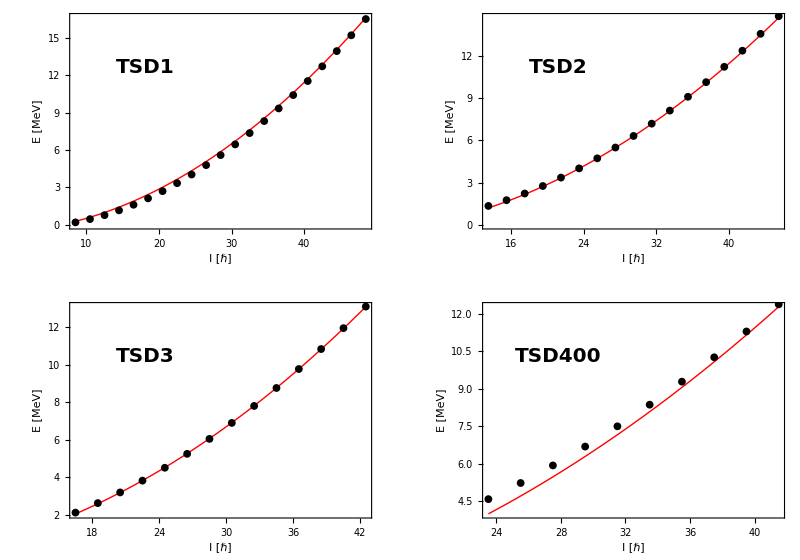

```mathematica
i1=77;i2=47;i3=3;v=2.1;γ=16;
grid[i1,i2,i3,v,γ,TSD400]
Export["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Reports/SIGNATURE_FORMALISM/tsd4_00_gridplot.png",grid[i1,i2,i3,v,γ,TSD400]];
```

```mathematica
rmsPrint[i1,i2,i3,v,γ,TSD400]
```

E_(RMS; TSD400)=0.197384

### tsd4-1,0

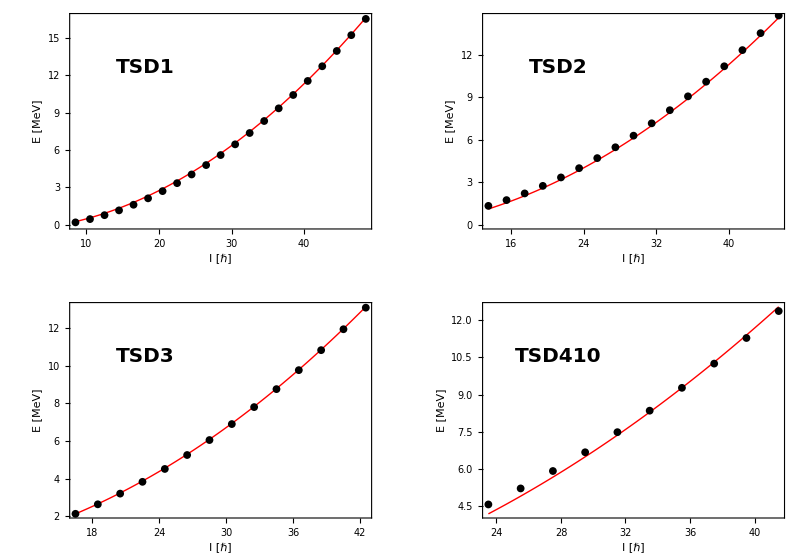

```mathematica
i1=73;i2=68;i3=3;v=8.1;γ=15;
grid[i1,i2,i3,v,γ,TSD410]
Export["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Reports/SIGNATURE_FORMALISM/tsd4_10_gridplot.png",grid[i1,i2,i3,v,γ,TSD410]];
```

```mathematica
rmsPrint[i1,i2,i3,v,γ,TSD410]
```

E_(RMS; TSD410)=0.138381

## Approaches that have valid minima inside the contour plot

## tsd4: 0-0

```mathematica
i1=52;i2=32;i3=48;v=9.1;γ=15;
contourGrid[i1_,i2_,i3_,v_,γ_]:=GraphicsGrid[{{p1[spinTSD1,IF[i1],IF[i2],IF[i3],v,γ],p1[spinTSD2,IF[i1],IF[i2],IF[i3],v,γ]},{p1[spinTSD3,IF[i1],IF[i2],IF[i3],v,γ],p1[spinTSD4,IF[i1],IF[i2],IF[i3],v,γ]}},ImageSize->Scaled[0.3],Frame->All];
```

```mathematica
contourGrid[i1,i2,i3,v,γ]
Export["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Reports/SIGNATURE_FORMALISM/full_contours.png",Show[contourGrid[i1,i2,i3,v,γ]]];
```